# Project Coding Template APPM 2350 : Spring 2018 Authors: Mattias Leino Derek Thomas

```mathematica
Clear["Global`*"]
```

```mathematica
$MinPrecision = 10;
```

## Section 3: Observers at three different latitudes

```mathematica
(* Functions *)
Θ[t_] := -0.41 * Cos[(2π*t)/ 365.25]
x[t_,ϕ_] := Cos[ϕ] * Sin[2π*t]
y[t_,ϕ_] := -Cos[ϕ] * Cos[2π*t] * Cos[Θ[t]] + Sin[ϕ] * Sin[Θ[t]]
z[t_, ϕ_] := Cos[ϕ] * Cos[2π * t] * Sin[Θ[t]] + Sin[ϕ] * Cos[Θ[t]]
n[t_,ϕ_] := Cos[ϕ] * Sin[Θ[t]] + Sin[ϕ] * Cos[Θ[t]] * Cos[2 * π * t]
e[t_, ϕ_] := Cos[Θ[t]] * Sin[2 * π * t]
u[t_, ϕ_] := (1 - n[t,ϕ]^2 - e[t,ϕ]^2)^(1/2)
η[t_, ϕ_] := ArcSin[u[t,ϕ]]
```

```mathematica
(* Latitudes of the locations we are looking at *)
boulderLat = 0.6981;
chichenitzaLat = 0.3613;
southpoleLat = 1.5708;
```

This is a plot of the position of the sun above and below the horizon (y=0) over the course of 5 days.

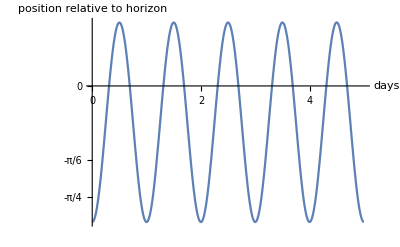

```mathematica
Plot[{y[t,0.698132]},{t,0,5}, AxesLabel->{"days","position relative to horizon"}, Ticks->{{0,1,2,3,4,5},{-π/4, -π/6,0,π/6,π/4}}]
```

```mathematica
(* Using the FindRoot fucntion to build a table of all the times the y(t,ϕ) function finds zero. i.e. When the sun crosses the horizon, either sunrise or sunset *)
days ={t} /. Table[FindRoot[y[t,boulderLat]==0, {t, day -0.25}], {day, 0.5, 365,0.5}] ;
Grid[days, Frame-> All]

(*creates a list of day lengths *)
riseIndex = 1;
setIndex = 2;
rise = 0;
set = 0;
dayLengths = {};
(*Loop iterates through each sunrise and sunset and finds the difference
then stores these differences in a list called day lengths*)
While[riseIndex < 730, 
rise = Part[days,riseIndex]; 
set = Part[days, setIndex]; 
AppendTo[dayLengths,(set-rise)];
 riseIndex = riseIndex+2; setIndex = setIndex+2];

(*some tests + printing min and max*)
dayLengths;
Length[dayLengths];
Max[dayLengths]
Position[dayLengths,Max[dayLengths]]
Min[dayLengths]
Position[dayLengths,Min[dayLengths]]

(* find the closest absolute distance to .5 *)
findEquinox[loopStart_,loopEnd_] :=(
candidate = 0;
currentMin =1;
For[i=loopStart, i < loopEnd, i++,
candidate = Part[dayLengths,i];
currentMin = If[(Abs[.5 - candidate]) < (Abs[.5-currentMin]), candidate, currentMin]
]
Return[currentMin];
)
equinox = findEquinox[1,180];
```

0.309409
0.690595
1.30939
1.69062
2.30935
2.69066
3.3093
3.69073
4.30922
4.69082
5.30912
5.69092
6.309
6.69105
7.30886
7.6912
8.3087
8.69137
9.30852
9.69156
10.3083
10.6918
11.3081
11.692
12.3079
12.6922
13.3076
13.6925
14.3073
14.6928
15.307
15.6931
16.3067
16.6934
17.3064
17.6938
18.306
18.6941
19.3056
19.6945
20.3053
20.6949
21.3048
21.6953
22.3044
22.6958
23.304
23.6962
24.3035
24.6967
25.303
25.6971
26.3026
26.6976
27.302
27.6982
28.3015
28.6987
29.301
29.6992
30.3004
30.6998
31.2999
31.7004
32.2993
32.701
33.2987
33.7016
34.2981
34.7022
35.2974
35.7028
36.2968
36.7035
37.2962
37.7041
38.2955
38.7048
39.2948
39.7055
40.2941
40.7062
41.2934
41.7069
42.2927
42.7076
43.292
43.7083
44.2913
44.709
45.2905
45.7098
46.2898
46.7105
47.289
47.7113
48.2883
48.7121
49.2875
49.7129
50.2867
50.7136
51.2859
51.7144
52.2851
52.7152
53.2843
53.7161
54.2835
54.7169
55.2826
55.7177
56.2818
56.7186
57.281
57.7194
58.2801
58.7202
59.2793
59.7211
60.2784
60.722
61.2776
61.7228
62.2767
62.7237
63.2758
63.7246
64.2749
64.7255
65.2741
65.7263
66.2732
66.7272
67.2723
67.7281
68.2714
68.729
69.2705
69.7299
70.2696
70.7308
71.2687
71.7318
72.2678
72.7327
73.2668
73.7336
74.2659
74.7345
75.265
75.7354
76.2641
76.7364
77.2632
77.7373
78.2622
78.7382
79.2613
79.7391
80.2604
80.7401
81.2594
81.741
82.2585
82.7419
83.2576
83.7429
84.2566
84.7438
85.2557
85.7448
86.2548
86.7457
87.2538
87.7466
88.2529
88.7476
89.2519
89.7485
90.251
90.7495
91.2501
91.7504
92.2491
92.7514
93.2482
93.7523
94.2472
94.7532
95.2463
95.7542
96.2454
96.7551
97.2444
97.7561
98.2435
98.757
99.2425
99.7579
100.242
100.759
101.241
101.76
102.24
102.761
103.239
103.762
104.238
104.763
105.237
105.764
106.236
106.764
107.235
107.765
108.234
108.766
109.233
109.767
110.232
110.768
111.231
111.769
112.231
112.77
113.23
113.771
114.229
114.772
115.228
115.773
116.227
116.774
117.226
117.774
118.225
118.775
119.224
119.776
120.223
120.777
121.223
121.778
122.222
122.779
123.221
123.78
124.22
124.781
125.219
125.781
126.218
126.782
127.217
127.783
128.217
128.784
129.216
129.785
130.215
130.785
131.214
131.786
132.213
132.787
133.213
133.788
134.212
134.789
135.211
135.789
136.21
136.79
137.21
137.791
138.209
138.792
139.208
139.792
140.207
140.793
141.207
141.794
142.206
142.794
143.205
143.795
144.205
144.796
145.204
145.796
146.203
146.797
147.203
147.798
148.202
148.798
149.201
149.799
150.201
150.8
151.2
151.8
152.2
152.801
153.199
153.801
154.199
154.802
155.198
155.802
156.198
156.803
157.197
157.803
158.197
158.804
159.196
159.804
160.196
160.805
161.195
161.805
162.195
162.805
163.194
163.806
164.194
164.806
165.194
165.807
166.193
166.807
167.193
167.807
168.193
168.807
169.192
169.808
170.192
170.808
171.192
171.808
172.192
172.808
173.192
173.809
174.191
174.809
175.191
175.809
176.191
176.809
177.191
177.809
178.191
178.809
179.191
179.809
180.191
180.809
181.191
181.809
182.191
182.809
183.191
183.809
184.191
184.809
185.191
185.809
186.191
186.809
187.191
187.809
188.191
188.809
189.191
189.809
190.191
190.809
191.191
191.809
192.192
192.808
193.192
193.808
194.192
194.808
195.192
195.808
196.192
196.807
197.193
197.807
198.193
198.807
199.193
199.806
200.194
200.806
201.194
201.806
202.194
202.805
203.195
203.805
204.195
204.804
205.196
205.804
206.196
206.804
207.197
207.803
208.197
208.803
209.198
209.802
210.198
210.802
211.199
211.801
212.199
212.8
213.2
213.8
214.2
214.799
215.201
215.799
216.201
216.798
217.202
217.798
218.203
218.797
219.203
219.796
220.204
220.796
221.205
221.795
222.205
222.794
223.206
223.794
224.207
224.793
225.207
225.792
226.208
226.791
227.209
227.791
228.21
228.79
229.21
229.789
230.211
230.788
231.212
231.788
232.213
232.787
233.214
233.786
234.214
234.785
235.215
235.784
236.216
236.784
237.217
237.783
238.218
238.782
239.218
239.781
240.219
240.78
241.22
241.779
242.221
242.779
243.222
243.778
244.223
244.777
245.224
245.776
246.224
246.775
247.225
247.774
248.226
248.773
249.227
249.772
250.228
250.771
251.229
251.771
252.23
252.77
253.231
253.769
254.232
254.768
255.233
255.767
256.233
256.766
257.234
257.765
258.235
258.764
259.236
259.763
260.237
260.762
261.238
261.761
262.239
262.76
263.24
263.76
264.241
264.759
265.242
265.758
266.243
266.757
267.244
267.756
268.245
268.755
269.246
269.754
270.247
270.753
271.247
271.752
272.248
272.751
273.249
273.75
274.25
274.749
275.251
275.748
276.252
276.747
277.253
277.746
278.254
278.745
279.255
279.745
280.256
280.744
281.257
281.743
282.258
282.742
283.259
283.741
284.26
284.74
285.261
285.739
286.262
286.738
287.262
287.737
288.263
288.736
289.264
289.735
290.265
290.734
291.266
291.733
292.267
292.732
293.268
293.732
294.269
294.731
295.27
295.73
296.271
296.729
297.272
297.728
298.273
298.727
299.273
299.726
300.274
300.725
301.275
301.724
302.276
302.724
303.277
303.723
304.278
304.722
305.279
305.721
306.28
306.72
307.28
307.719
308.281
308.718
309.282
309.718
310.283
310.717
311.284
311.716
312.285
312.715
313.285
313.714
314.286
314.714
315.287
315.713
316.288
316.712
317.289
317.711
318.289
318.71
319.29
319.71
320.291
320.709
321.292
321.708
322.292
322.707
323.293
323.707
324.294
324.706
325.294
325.705
326.295
326.705
327.296
327.704
328.296
328.703
329.297
329.703
330.298
330.702
331.298
331.701
332.299
332.701
333.299
333.7
334.3
334.7
335.301
335.699
336.301
336.699
337.302
337.698
338.302
338.698
339.303
339.697
340.303
340.697
341.304
341.696
342.304
342.696
343.305
343.695
344.305
344.695
345.305
345.694
346.306
346.694
347.306
347.694
348.306
348.693
349.307
349.693
350.307
350.693
351.307
351.692
352.308
352.692
353.308
353.692
354.308
354.692
355.308
355.692
356.309
356.691
357.309
357.691
358.309
358.691
359.309
359.691
360.309
360.691
361.309
361.691
362.309
362.691
363.309
363.691
364.309
364.691

0.618818

{{183,1}}

0.381186

{{1,1}}

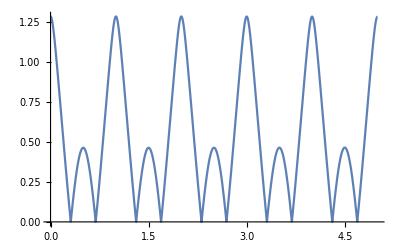

```mathematica
Plot[{η[t,0.698132]},{t,0,5}]
```

```mathematica
(* *)
RiseAngle[dayRA_,phiRA_] := 
(srtRA = FindRoot[y[tRA, phiRA] == 0, {tRA, Round[dayRA] -0.75}];
180*ArcCos[n[tRA/.srtRA,phiRA]]/Pi);
```

```mathematica
boulderRA = Table[RiseAngle[dayRA,40*Pi/180],{dayRA,0,365,1}];
```

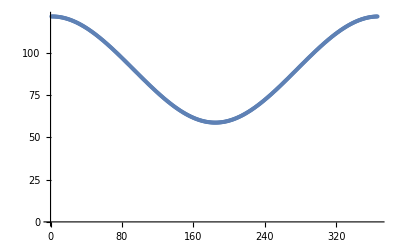

```mathematica
ListPlot[boulderRA]
```

```mathematica
mexicoDays ={t} /. Table[FindRoot[y[t,chichenitzaLat]==0, {t, day -0.25}], {day, 0.5, 365,0.5}] ;


(*creates a list of day lengths *)
riseIndex = 1;
setIndex = 2;
rise = 0;
set = 0;
dayLengths = {};
While[riseIndex < 730, 
rise = Part[mexicoDays,riseIndex]; 
set = Part[mexicoDays, setIndex]; 
AppendTo[dayLengths,(set-rise)];
 riseIndex = riseIndex+2; setIndex = setIndex+2];

(*some tests + printing min and max*)
dayLengths;
Length[dayLengths];
Max[dayLengths]
Position[dayLengths,Max[dayLengths]]
Min[dayLengths]
Position[dayLengths,Min[dayLengths]]

(* find the closest absolute distance to .5 *)
findEquinox[loopStart_,loopEnd_] :=(
candidate = 0;
currentMin =1;
For[i=loopStart, i < loopEnd, i++,
candidate = Part[dayLengths,i];
currentMin = If[(Abs[.5 - candidate]) < (Abs[.5-currentMin]), candidate, currentMin]
]
Return[currentMin];
)
equinox = findEquinox[1,180];
```

0.552517

{{183,1}}

0.447485

{{1,1}}

```mathematica
southPoleDays ={t} /. Table[FindRoot[y[t,southpoleLat]==0, {t, day -0.25}], {day, 0.5, 365,0.5}] ;

(*creates a list of day lengths *)
riseIndex = 1;
setIndex = 2;
rise = 0;
set = 0;
dayLengths = {};
While[riseIndex < 730, 
rise = Part[southPoleDays,riseIndex]; 
set = Part[southPoleDays, setIndex]; 
AppendTo[dayLengths,(set-rise)];
 riseIndex = riseIndex+2; setIndex = setIndex+2];

(*some tests + printing min and max*)
dayLengths;
Length[dayLengths];
Max[dayLengths]
Position[dayLengths,Max[dayLengths]]
Min[dayLengths]
Position[dayLengths,Min[dayLengths]]

(* find the closest absolute distance to .5 *)
findEquinox[loopStart_,loopEnd_] :=(
candidate = 0;
currentMin =1;
For[i=loopStart, i < loopEnd, i++,
candidate = Part[dayLengths,i];
currentMin = If[(Abs[.5 - candidate]) < (Abs[.5-currentMin]), candidate, currentMin]
]
Return[currentMin];
)
equinox = findEquinox[1,180];
```

730.5

{{186,1}}

-3469.87

{{182,1}}

## Section 4: Radiant flux and the seasons

```mathematica
r[t_,ϕ_] := {x[t,ϕ],y[t,ϕ],z[t,ϕ]};
Flux[t1_,t2_,t_,ϕ_] := ∫_t1^t2 Dot[{0,1,0},r[t,ϕ]]ⅆt;

(* Calculating absolute error introduced by treating sun as a point source *)
```

```mathematica
sunDiameter = 2*7.0*10^5;
earthToSun = 1.5 * 10^8;

(* calculating maximum relative error of earth sun distance introduced by treating earth's orbit as circular *)

(* using values from tables create a table of *)
```

# Appendix

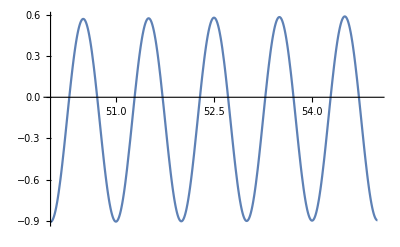

```mathematica
Plot[{y[t,0.698132]},{t,50,55}]
```

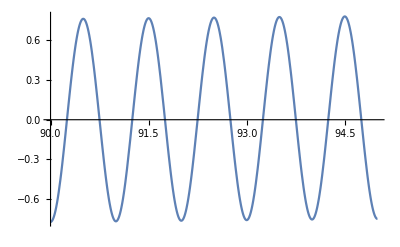

```mathematica
Plot[{y[t,0.698132]},{t,90,95}]
```

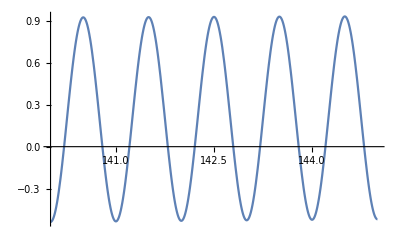

```mathematica
Plot[{y[t,0.698132]},{t,140,145}]
```

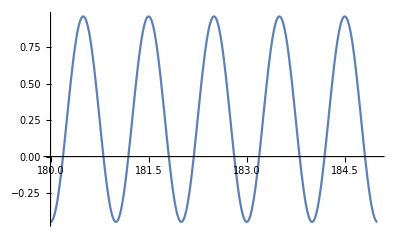

```mathematica
Plot[{y[t,0.698132]},{t,180,185}]
```

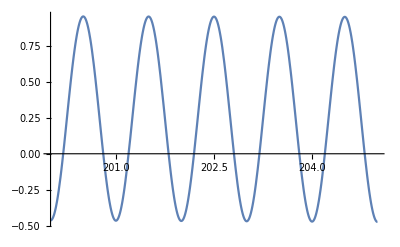

```mathematica
Plot[{y[t,0.698132]},{t,200,205}]
```

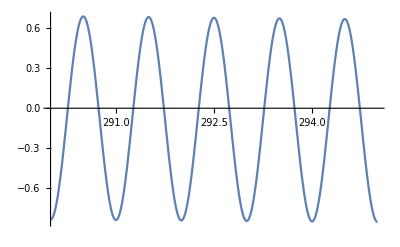

```mathematica
Plot[{y[t,0.698132]},{t,290,295}]
```

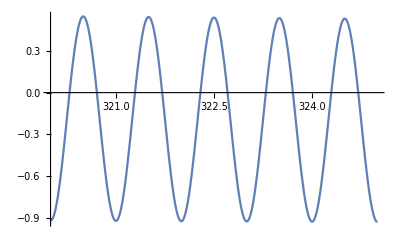

```mathematica
Plot[{y[t,0.698132]},{t,320,325}]
```